```mathematica
$HistoryLength=1;
Needs["Developer`"]
Needs["DiffusiveDynamics`"]

$VerbosePrint=True;

R[α_]:={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};
DDD[Dx_,Dy_]:={{1/Dx^2,0},{0,1/Dy^2}};
D2DMat[Dx_,Dy_,α_]:=N[Evaluate[R[α °].DDD[Dx,Dy].Transpose[R[α °]]]];
```

```mathematica
STEPS=1000000;
STEP=1;
CELLRANGE={1000.,500.};

ClearAll[DIFFX,DIFFY,ALPHA];



DIFFX=Compile[{x,y},
1];
DIFFY=Compile[{x,y},
5];

DIFFX=Compile[{x,y},
5Sin[x/ CELLRANGE[[1]] π] +10];
DIFFY=Compile[{x,y},
5Sin[y/ CELLRANGE[[2]] π] +10];


ALPHA=Compile[{x,y},0];
ALPHA=Compile[{x,y},
(((x/2)/CELLRANGE[[1]])^2+((y/2)/ CELLRANGE[[2]])^2)*180];
TENSOR[x_,y_]:=D2DMat[DIFFX[x,y],DIFFY[x,y],ALPHA[x,y]];
ClearAll[ENERGY]; (*energija v enotah kT*)
ENERGY=Compile[{x,y},1];
KT=1.;
```

```mathematica
CELL$plots=DiffusionParameters2DPlots[DIFFX,DIFFY,ALPHA,ENERGY,CELLRANGE]
StringForm["STEPS `1`; STEP `2`; KT `3`",STEPS,STEP,KT]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

STEPS 1000000; STEP 1; KT 1.

```mathematica
.
```

```mathematica
$VerbosePrint=True;
```

```mathematica
AbsoluteTiming[
rw=GenerateDiffusionTrajectory2D[STEPS,DIFFX,DIFFY,ALPHA,ENERGY,KT,STEP,{-CELLRANGE,CELLRANGE},Verbose->True,InitialPosition->{0,0}];
]
rw[[;;10]]
```

{2.85616,Null}

{{1,0.,0.},{2,-0.834234,-4.69813},{3,-3.18478,-6.24758},{4,-2.53955,1.53677},{5,1.83371,2.04304},{6,-0.435945,3.98999},{7,-4.18993,1.61461},{8,3.2835,1.46224},{9,7.46896,-0.989535},{10,4.65245,1.55465}}

```mathematica
AbsoluteTiming[
rw=ParallelGenerateDiffusionTrajectory2D[STEPS,DIFFX,DIFFY,ALPHA,ENERGY,KT,STEP,{-CELLRANGE,CELLRANGE},"ThreadCount"->1];
]
```

{3.7972172,Null}

```mathematica
StrideData[rw[[1,1;;100]],20]
```

20

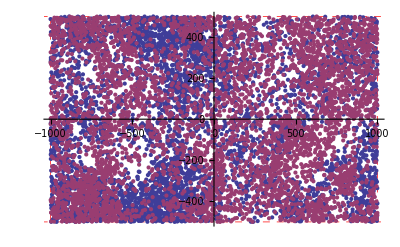

```mathematica
ListPlot[rw[[All,;;;;Ceiling[STEPS/10000],{2,3}]],PlotRange->All,GridLines->Transpose@{-CELLRANGE,CELLRANGE},GridLinesStyle->Directive[Red,Thick,Dashed]]
```